# NG4P10 Dyploid genetic algorithms.

Выполнила  студентка 2 курса  5 группы
Кадакова Надежда
15.05.2017

Основной принцип работы диплоидных генетических алгоритмов заключается в возможности кодирования одних и тех же свойств особи (переменных) хромосомными наборами, полученными от обоих родителей. При этом проявляются свойства в дочерней особи в зависимости от отношений доминантности и рецессивности между гомологичными (находящимися в одинаковых позициях) генами родительских хромосом.

## Ex.1

Рассмотрим двухмерное фазовое пространство -500 ⩽ x, y ⩽ 500. Из файла «NG17P10Problem.mx»
загрузите две карты Troubles[0][x, y] и Troubles[1][x, y] (см. Рис.1 и Рис.2), изобразите обе карты
графически, используя один из операторов DensityPlot или ContourPlot и цветовую палитру
ColorFunction → “GreenPinkTones”.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<NG17P10Problem.m
```

```mathematica
?Troubles
```

Troubles[0][x,y] — начальная и Troubles[1][x,y] — финальная карты, определённые на двухмерном фазовом пространстве -500 ⩽ x,y ⩽ +500

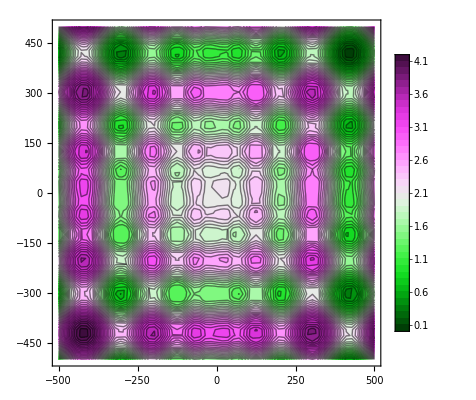

```mathematica
T1=ContourPlot[Troubles[1][x,y],{x,-500,500},{y,-500,500},ColorFunction->"GreenPinkTones",Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic]
```

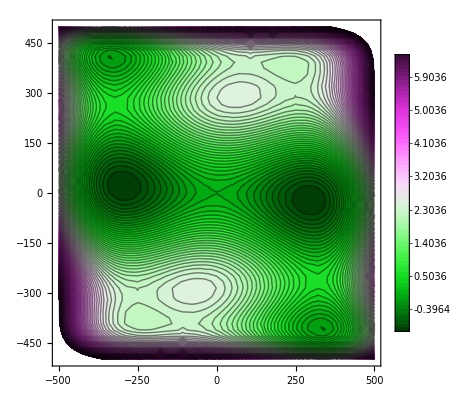

```mathematica
T0=ContourPlot[Troubles[0][x,y],{x,-500,500},{y,-500,500},ColorFunction->"GreenPinkTones",Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic]
```

В таком случае проблемные (малопригодные для жизни) участки будут отмечены густо розовым цветом, а благоприятные для жизни участки — густо зеленым (см. Рис.3). Рассчитайте, какой должна быть длина хромосомы, чтобы точность найденного решения составляла не менее трёх десятичных разрядов после запятой. Используя полученный результат, дискретизируйте фазовое пространство.

```mathematica
MinPoint=1000/0.001//N;
```

Дискретизируем фазовое пространство:
Для того  чтобы точность  составляла  3  знака  после  запятой разобьем пространство  на ((1/0.001)*1000)^2= 10^12 квадратов.

Рассчитаем  длину хромосомы каждой особи:

```mathematica
L=Ceiling[Log[2,(1000/0.001)^2]//N]
```

40

Напишем  соответственно функции перевода  точки в квадрат и  обратно:

```mathematica
PointToSquare[{x_,y_}]:=Module[{dx=MinPoint/2},
Round[N[(Ceiling[x/0.001]+dx)+((Ceiling[y/0.001]+dx)*MinPoint)]]
]
```

```mathematica
PointToSquare[{500,497}]
```

997001000000

```mathematica
SquareTorandomPoint[n_]:=Module[{x=Mod[n,MinPoint],y=Quotient[n,MinPoint],xf,yf,dx=MinPoint/2},
xf=RandomReal[{(x-dx)*0.001+0.001,(x-dx)*0.001}];yf=RandomReal[{(y-dx)*0.001+0.001,(y-dx)*0.001}];
{xf,yf}]
```

```mathematica
SquareTorandomPoint[PointToSquare[{500,497}]]
```

{-499.999,497.002}

## Ex.2

Сконструируйте хромосому диплоидной особи, используя код Грея (см. [2], п.1.3, сс.40–41) для кодирования фенотипа и четырёхбуквенный алфавит:

0(r) – отсутствие рецессивного признака,
1(R) – наличие рецессивного признака,
2(d) – отсутствие доминантного признака,
3(D) – наличие доминантного признака, 
— для кодирования генотипа. Реализуйте процедуру перехода от генотипа к фенотипу (см. [1], п.5, сс.56–57).

Функции кодирования и декодирования в код Грэя:

```mathematica
IntegerToGrayCode[k_]:=Module[{b=IntegerDigits[k,2],i,l,add={}},
Do[
If[b⟦i-1⟧==1,b⟦i⟧=1-b⟦i⟧],
{i,Length[b],2,-1}
];
l=Length[b];
If[Length[b]<40,
For[i=1,i≤(40-l),i++,b=Prepend[b,0]
]];
b
]
```

```mathematica
GrayCodeToInteger[d_]:=Module[{b=d,i,j},
Do[
If[Mod[Sum[b[[j]],{j,i-1}],2]==1,
b[[i]]=1-b[[i]]],
{i,Length[d],2,-1}
];
FromDigits[b,2]
]
```

```mathematica
IntegerToGrayCode[PointToSquare[{500,497}]]
```

{1,0,0,1,1,1,0,0,0,0,1,1,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,0,1,1,0,0,0,0,0}

```mathematica
GrayCodeToInteger[%]
```

997001000000

Функция  преобразования генотипа в фенотип:

```mathematica
GTF[g_]:=Module[{t,r={},res},
Do[t=g[[1,j]]<>g[[2,j]];
r=Append[r,StringReplace[t,{"rr"->"0","rR"->"1","rd"->"0","rD"->"1","Rr"->"0","RR"->"1","Rd"->"0","RD"->"1","dr"->"0","dR"->"0","dd"->"0","dD"->"0","Dr"->"1","DR"->"1","Dd"->"1","DD"->"1"}]]
,{j,1,Length[g[[1]]]}];
res=ToExpression[#]&/@r;
res
]
```

```mathematica
GTF[{{"D","r","r","R"},{"D","r","r","R"}}]
```

{1,0,0,1}

Функция перевода хромосомы в точку:

```mathematica
ChromosomeToPoint[chromosome_]:=SquareTorandomPoint[GrayCodeToInteger[GTF[chromosome]]];
```

```mathematica
ChromosomeToPoint[{{"D","r","r","R"},{"D","r","r","R"}}]
```

{-499.986,-499.999}

```mathematica
ChromosomeToPointPopulation[pop_]:=ChromosomeToPoint[#]&/@pop;
```

## Ex.3

Реализуйте генетические операции: мутацию (Mutation), инверсию (Inversion) и скрещивание (Crossover), — над диплоидными особями. Проверьте (визуально) действие каждого из операторов на популяцию в течение нескольких поколений.

Зададим  случайному популяцию для  проверки  работы функций  мутации,  инверсии и  скрещивания

```mathematica
RandomPopulation[n_]:=Table[Table[RandomChoice[{"r","R","d","D"},L],{i,1,2}],{j,1,n}]
```

```mathematica
FirstPopulation=RandomPopulation[50];
```

Функция мутации одной  особи:

```mathematica
Mutation[chromosome_]:=Module[{k1=chromosome[[1]],k2=chromosome[[2]],i=RandomInteger[{1,Length[chromosome[[1]]]}],j=RandomInteger[{1,Length[chromosome[[1]]]}],res={}},
k1[[i]]=RandomChoice[{"r","R","d","D"}];
k1[[j]]=RandomChoice[{"r","R","d","D"}];
res={k1,k2}
];
```

```mathematica
Mutation[FirstPopulation[[1]]]
```

{{D,D,d,r,d,R,R,d,R,d,d,r,r,d,r,R,R,r,d,D,d,d,D,d,d,R,R,R,d,d,r,R,D,D,r,d,d,d,D,r},{r,d,d,R,R,R,D,d,D,r,d,d,D,R,D,d,D,r,d,D,r,D,d,D,d,r,r,D,r,R,D,R,D,D,R,d,D,r,d,r}}

Функция мутации популяции:

```mathematica
MutationPopulation[population_]:=Module[{c,pop=population},
For[i=1, i≤Length[pop],i++,
c=RandomChoice[{0.1,0.9}->{1,0}];
If[c==1,
pop[[i]]=Mutation[pop⟦i⟧];]
];
pop
];
```

Проверим визуально  функцию мутации в  течении  10  поколений:

```mathematica
Show1Pop=ChromosomeToPoint[#]&/@FirstPopulation;
```

```mathematica
MutationPopulation[FirstPopulation];
```

```mathematica
mutF=NestList[MutationPopulation,FirstPopulation,10];
```

```mathematica
ShowMut=ChromosomeToPoint[#]&/@mutF[[9]];
```

Начальная  популяция:

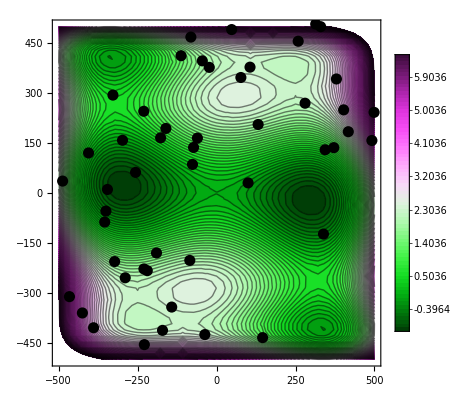

```mathematica
Show[T0,Graphics[{Black,PointSize[0.02],Point[#]&/@Show1Pop,
Thickness[0.02]}, {Frame -> True}]]
```

Мутированная  популяция:

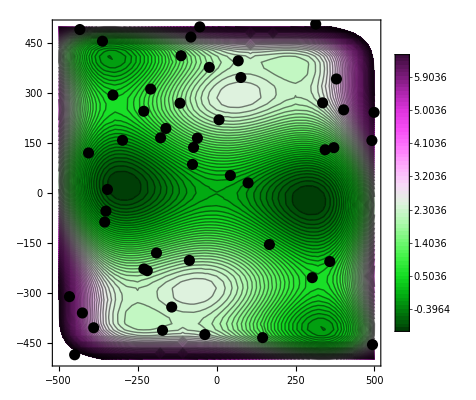

```mathematica
Show[T0,Graphics[{Black,PointSize[0.02],Point[#]&/@ShowMut,
Thickness[0.02]}, {Frame -> True}]]
```

Функция  инверсии для одной  особи:

```mathematica
Inversion[chromosome_,part_]:=Module[{ch1=chromosome[[1]],ch2=chromosome[[2]],r,res},
res={Join[ch1⟦part+1;;Length[ch1]⟧,ch1⟦1;;part⟧],Join[ch2⟦part+1;;Length[ch2]⟧,ch2⟦1;;part⟧]}
]
```

```mathematica
Inversion[FirstPopulation[[1]],2]
```

{{d,r,d,R,R,d,R,d,d,r,r,D,r,R,R,r,d,D,d,d,D,d,d,r,R,R,d,d,r,R,D,D,r,d,d,d,D,r,D,D},{d,R,R,R,D,d,D,r,d,d,D,R,D,d,D,r,d,D,r,D,d,D,d,r,r,D,r,R,D,R,D,D,R,d,D,r,d,r,r,d}}

Функция  инверсии  для  популяции:

```mathematica
InversionPupulation[population_]:=Module[{c,k,pop=population},
For[i=1, i≤Length[pop],i++,
c=RandomChoice[{0.01,0.99}->{1,0}];
If[c==1,
k=RandomInteger[Length[pop[[i,1]]]];
pop[[i]]=Inversion[pop[[i]],k]]];
pop
]
```

Проверим  визуально инверсию популяции в  течении  10  поколений:

```mathematica
invF=NestList[InversionPupulation,FirstPopulation,10];
```

```mathematica
ShowInv=ChromosomeToPoint[#]&/@invF[[9]];
```

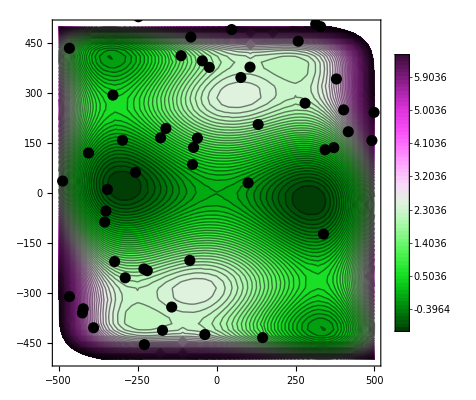

```mathematica
Show[T0,Graphics[{Black,PointSize[0.02],Point[#]&/@ShowInv,
Thickness[0.02]}, {Frame -> True}]]
```

Для скрещивая нам понадобиться нахождение “наиболее сильной особи”. Для этого напишем функцию,  вычисляющую значение Troubles для отдельной особи:

```mathematica
TroublesChromosome[n_,chromosome_]:=Troubles[n][ChromosomeToPoint[chromosome][[1]],ChromosomeToPoint[chromosome][[2]]];
```

```mathematica
TroublesChromosome[0,FirstPopulation[[1]]]
TroublesChromosome[1,FirstPopulation[[1]]]
```

0.595988

2.26781

Функция скрещивания двух особей:

```mathematica
Crossover[chromosome1_,chromosome2_,n_]:=
Module[{
n1=RandomInteger[{1,Length@chromosome1[[1]]}],
n2=RandomInteger[{1,Length@chromosome2[[1]]}],
ch1=chromosome1,
ch2=chromosome2,
res1,res2,res,
k1,k2},
k1=TroublesChromosome[n,ch1];
k2=TroublesChromosome[n,ch2];
If[k1>k2,
res1=Join[ch1[[1,1;;n1]],ch1[[2,n1+1;;Length@ch1[[2]]]]];
res2=Join[ch2[[1,1;;n2]],ch2[[2,n2+1;;Length@ch2[[2]]]]],
res1=Join[ch2[[1,1;;n2]],ch1[[2,n2+1;;Length@ch2[[2]]]]];
res2=Join[ch1[[1,1;;n1]],ch1[[2,n1+1;;Length@ch1[[2]]]]]
];
res={res1,res2}
]
```

```mathematica
Crossover[FirstPopulation[[1]],FirstPopulation[[2]],0]
```

{{D,D,d,r,d,R,R,d,R,d,d,r,r,D,r,R,R,r,d,D,r,D,d,D,d,r,r,D,r,R,D,R,D,D,R,d,D,r,d,r},{r,D,d,r,d,D,d,r,D,D,r,r,R,R,R,D,r,D,r,D,R,d,d,R,r,r,d,r,d,r,r,r,d,d,D,d,R,d,R,r}}

Функция скрещивания популяции:

```mathematica
CrossoverPopulation[population_,n_]:=Module[{pop=population,res={},c1,c2},
Do[
c1=RandomInteger[{1,Length@pop}];
c2=RandomInteger[{1,Length@pop}];
AppendTo[res,Crossover[pop[[c1]],pop[[c2]],n]];
,{i,1,Length@pop}];
res
]
```

Проверим  визуально  скрещивание  популяции  в  течении  10 поколений:

```mathematica
CrossoverPopulation[FirstPopulation,0];
```

```mathematica
crossF=NestList[CrossoverPopulation[#,1]&,FirstPopulation,10];
```

```mathematica
Showcross=ChromosomeToPoint[#]&/@crossF[[9]];
```

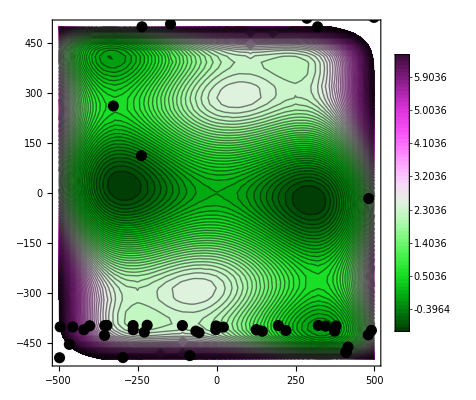

```mathematica
Show[T0,Graphics[{Black,PointSize[0.02],Point[#]&/@Showcross,
Thickness[0.02]}, {Frame -> True}]]
```

## Ex.4

Сгенерируйте 50 случайных точек, равномерно распределённых по фазовому пространству. На основе этих точек создайте две популяции : гаплоидную, назовем её HGA, и диплоидную, назовём её DGA. Функцию приспособленности Fitness и репродуктивный план перенесите из предыдущей лабораторной NG16P10 без изменений.

```mathematica
DGA=RandomPopulation[50];
```

```mathematica
HGA=ChromosomeToPoint[#]&/@DGA;
```

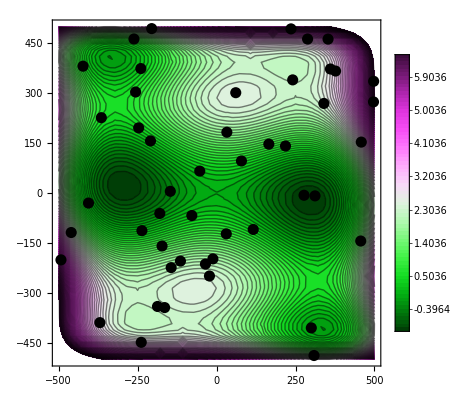

```mathematica
Show[T0,Graphics[{Black,PointSize[0.02],Point[#]&/@HGA,
Thickness[0.02]}, {Frame -> True}]]
```

```mathematica
Show[T1,Graphics[{Black,PointSize[0.02],Point[#]&/@HGA,
Thickness[0.02]}, {Frame -> True}]]
```

-Graphics-

Напишем  функцию приспособленности  для  диплоидного  алгоритма:
Будем  выбирать 50  наиболее  приспособленных особей.
Приспособленность  считаем написанной выше  функцией TroublesChromosome.

```mathematica
FitnessDip[population_,n_]:=Module[{pop=population,tr,sortedpop={},temp={},s={},res={}},
temp=SortBy[Flatten[Table[Append[sortedpop,{pop⟦i⟧,TroublesChromosome[n,pop[[i]]]}],{i,1,Length[pop]}],1],Last];
sortedpop=Delete[#,2]&/@temp;
s=Flatten[sortedpop,1];
res=s[[1;;50]]
]
```

Реализуем репродуктивный  план для диплоидной популяции:

```mathematica
Evolution[population_,n_]:=FitnessDip[Join[MutationPopulation[population],InversionPupulation[population],CrossoverPopulation[population,n]],n];
```

## Ex.5

Первый этап соревнования. Каждым из двух генетических алгоритмов HGA и DGA найдите минимум на начальной карте Troubles[0] (см. Рис.1). Запишите количество поколений, время работы алгоритма и абсолютную погрешность полученного результата.

С помощью функции  Animate отобразим графически работу алгоритма DGA по  нахождению  минимума на  Карте Troubles[0].

```mathematica
ten=NestList[Evolution[#,0]&,DGA,6];
tenEv=ChromosomeToPointPopulation[#]&/@ten;
Animate[Show[T0,Graphics[{Black,PointSize[0.02],Point[#]}]&/@tenEv[[u]]]
,{u,1,Length@tenEv,1},AnimationRunning->False]
```

Заметим,  что при работе  диплоидного  алгоритма точки  сходятся за  6  поколений. 
А  по  результатам  прошлой  работы: при работе  гаплоидного  алгоритма - за 10  поколений.

## Ex.6

Второй этап соревнования. Каждый из алгоритмов HGA и DGA стартует из «своей» популяции, достигшей финала первого этапа, и находит минимум на финальной карте Troubles[1] (см. Рис.2). Запишите количество поколений, время работы алгоритма и абсолютную погрешность полученного результата. Сделайте выводы.

С помощью функции  Animate отобразим графически работу алгоритма DGA по  нахождению  минимума на  Карте Troubles[1].

```mathematica
ten1=NestList[Evolution[#,1]&,DGA,6];
```

```mathematica
fff=ChromosomeToPointPopulation[#]&/@ten1;
```

```mathematica
Animate[Show[T1,Graphics[{Black,PointSize[0.02],Point[#]}]&/@fff[[u]]]
,{u,1,Length@fff,1},AnimationRunning->False]
```

Такой же  результат(6  поколений) показывает диплоидный  алгоритм  и  на  карте Troubles[1];

## Conclusion

По  результатам данной  работы,  можно  сделать  вывод,  что  диплоидный  алгоритм  работает  быстрее с  точки зрения решения задачи,  т.е. дает  нужный  результат за 6 поколений,  по  сравнению  с гаплоидным, который дает  этот  же результат за 10  поколений. Также, среди различных преимуществ диплоидности особое внимание обращается на уменьшение скорости фенотипического вырождения популяции